```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/manuscript/graphs

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
dbg=False;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["/home/kirscher/Documents/vault/Vorlesungen/num_methods/lec_ex0_b2.22.dat","Table"]
```

{{#,lambda,2bd,C,(1,BS,at,2.2),3bd,D,(2BS,with,1ex,at,8.48),B(1ex,D=0)},{8.,-974.194,-1105.1,0.},{9.,-1090.46,-1183.62,0.},{10.,-1206.46,-1256.76,0.},{11.,-1322.21,-1363.1,0.},{12.,-1437.76,-1402.35,0.},{13.,-1553.2,-1457.85,0.},{14.,-1668.47,-1537.32,0.},{15.,-1783.52,-1560.86,0.},{16.,-1898.53,-1589.7,0.},{17.,-2013.44,-1682.78,0.},{18.,-2128.1,-1711.48,4.29},{19.,-2243.04,-1748.02,4.36},{20.,-2357.36,-1788.28,4.46},{21.,-2471.76,-1951.7,4.52},{22.,-2586.19,-1845.33,0.},{23.,-2700.54,-1866.45,0.},{24.,-2814.81,-1868.75,4.7},{25.,-2929.04,-1876.33,0.},{26.,-3043.2,-1896.75,4.88},{27.,-3157.31,-1925.78,0.},{28.,-3271.38,-1912.15,5.08},{29.,-3385.37,-1932.44,0.},{30.,-3499.32,-1964.75,0.},{31.,-3613.28,-1951.24,0.},{32.,-3727.18,-1971.84,0.},{33.,-3840.96,-1969.59,0.},{34.,-3954.94,-1980.64,0.},{35.,-4068.58,-1966.92,0.},{36.,-4182.67,-1919.66,0.},{37.,-4295.94,-1964.46,0.},{38.,-4409.67,-1973.3,5.62},{39.,-4523.22,-1937.47,0.},{40.,-4637.06,-1980.96,0.},{41.,-4750.43,-1916.56,0.},{42.,-4864.11,-1925.1,0.},{43.,-4978.46,-1.,0.},{44.,-5091.12,-1.,0.},{45.,-5205.08,-1.,0.},{46.,-5318.48,-1.,0.},{47.,-5431.89,-1.,0.},{48.,-5545.3,-1.,0.},{49.,-5658.17,-1.,0.},{50.,-5772.4,-1.,0.},{51.,-5885.2,-1.,0.},{52.,-5998.83,-1.,0.},{53.,-6112.24,-1.,0.},{54.,-6225.06,-1.,0.},{55.,-6339.32,-1.,0.},{56.,-6451.71,-1.,0.},{57.,-6564.58,-1.,0.},{58.,-6678.68,-1.,0.},{59.,-6791.54,-1.,0.},{60.,-6904.95,-1.,0.},{61.,-7018.53,-1.,0.},{62.,-7131.6,-1.,0.},{63.,-7244.76,-1.,0.},{64.,-7357.57,-1.,0.},{65.,-7471.38,-1.,0.},{66.,-7584.19,-1.,0.},{67.,-7696.75,-1.,0.},{68.,-7810.85,-1.,0.},{69.,-7923.8,-1.,0.},{70.,-8036.02,-1.,0.},{71.,-8149.91,-1.,0.},{72.,-8263.91,-1.,0.},{73.,-8376.02,-1.,0.},{74.,-8489.13,-1.,0.},{75.,-8603.73,-1.,0.},{76.,-8715.24,-1.,0.},{77.,-8827.83,-1.,0.},{78.,-8941.35,-1.,0.},{79.,-9053.81,-1.,0.},{80.,-9166.69,-1.,0.},{81.,-9279.2,-1.,0.},{82.,-9391.54,-1.,0.},{83.,-9506.95,-1.,0.},{84.,-9618.1,-1.,0.},{85.,-9732.95,-1.,0.},{86.,-9845.6,-1.,0.},{87.,-9957.92,-1.,0.},{88.,-10072.4,-1.,0.},{89.,-10184.1,-1.,0.},{90.,-10295.8,-1.,0.},{91.,-10407.7,-1.,0.},{92.,-10523.9,-1.,0.},{93.,-10633.5,-1.,0.},{94.,-10746.7,-1.,0.},{95.,-10862.1,-1.,0.},{96.,-10972.8,-1.,0.},{97.,-11085.5,-1.,0.},{98.,-11203.3,-1.,0.},{99.,-11313.2,-1.,0.},{100.,-11426.2,-1.,0.},{101.,-11534.3,-1.,0.},{102.,-11649.4,-1.,0.},{103.,-11765.5,-1.,0.},{104.,-11876.3,-1.,0.},{105.,-11987.,-1.,0.},{106.,-12101.8,-1.,0.},{107.,-12213.,-1.,0.},{108.,-12327.4,-1.,0.},{109.,-12441.4,-1.,0.},{110.,-12550.,-1.,0.},{111.,-12661.1,-1.,0.},{112.,-12775.3,-1.,0.},{113.,-12892.5,-1.,0.},{114.,-13004.7,-1.,0.},{115.,-13120.5,-1.,0.},{116.,-13228.9,-1.,0.},{117.,-13339.9,-1.,0.},{118.,-13452.5,-1.,0.},{119.,-13567.,-1.,0.},{120.,-13679.5,-1.,0.},{121.,-13789.3,-1.,0.},{122.,-13905.1,-1.,0.},{123.,-14016.4,-1.,0.},{124.,-14131.,-1.,0.},{125.,-14239.7,-1.,0.},{126.,-14351.,-1.,0.},{127.,-14471.,-1.,0.},{128.,-14584.2,-1.,0.},{129.,-14693.,-1.,0.},{130.,-14803.3,-1.,0.},{131.,-14915.9,-1.,0.},{132.,-15031.,-1.,0.},{133.,-15146.3,-1.,0.},{134.,-15251.5,-1.,0.},{135.,-15369.9,-1.,0.},{136.,-15479.1,-1.,0.},{137.,-15589.9,-1.,0.},{138.,-15704.3,-1.,0.},{139.,-15817.5,-1.,0.},{140.,-15930.3,-1.,0.},{141.,-16041.2,-1.,0.}}

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2 b2+4 lam))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] core[[k]][[1]] core[[l]][[1]] (1/2)^(9/2)(Pi/((core[[i]][[2]]+core[[j]][[2]]) (core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];


VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta1,eta2,eta3,w1,w2,w3},
eta1=(3Cc Pi^1.5)/(8(lam Bb+Gg(lam+2Bb)+lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh))^1.5);
w1=(2lam(Aa+Bb)(Gg+Hh))/(lam Bb+Gg(lam+2Bb)+lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh));
eta2=(Pi/((lam+Aa+Bb)(lam+Gg+Hh)))^(3/2)Dd(1/2)^(9/2);
w2=(2lam(Aa+Bb))/(lam+Aa+Bb);
eta3=Pi^1.5 Dd/(8(2 lam^2+lam Bb+Gg(5lam+2Bb)+5lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh))^(3/2));
w3=(2lam (2lam+Aa+Bb)(Gg+Hh))/(2 lam^2+lam Bb+Gg(5lam+2Bb)+5lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh));
eta1 Exp[-w1 r^2]+eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq,radMA},Block[{zeta1,zeta2,zeta3,zeta4,zeta5,zeta6,a1,b1,c1,a2,b2,c2,a3,b3,c3,a4,b4,c4,a5,b5,c5,a6,b6,c6,Sinh1,Sinh2,Sinh3,Sinh4,Sinh5,Sinh6,CoshA},
zeta1=-(Pi/(2(Aa+Bb+Gg+Hh)))^(3/2)(1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(π^(3/2)/(2 √2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);
zeta3=-(π^(3/2)/(2 √2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);
zeta4=-(π^(3/2)/(2 √2)) Cc/(Aa +Bb+ Gg+Hh)^(3/2);
zeta5=-(Pi/(2(4lam+Aa+Bb+Gg+Hh)))^(3/2)Dd;
zeta6=-(Pi/(2(2lam+Aa+Bb+Gg+Hh)))^(3/2)Dd;

a2=(4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a4= (2lam Hh+2Bb(lam+2Hh)+Gg(2lam+Bb+Hh)+Aa(Bb+2lam+Hh))/(2(Aa+Bb+Gg+Hh));
b4= (4lam Hh+4lam Bb+Gg(4lam +2Bb-2Hh)+Aa(-2Bb+4lam+2Hh))/(2(Aa+Bb+Gg+Hh));
c4=(2lam Hh+2lam Bb+Gg(2lam+Bb+Hh)+Aa(4Gg+Bb+2lam+Hh))/(2(Aa+Bb+Gg+Hh));

a5=(2lam(2lam+Hh)+2Bb(5lam+2Hh)+Gg(2lam+Bb+Hh)+Aa(Bb+2lam+Hh))/(2(4lam+Aa+Bb+Gg+Hh));
b5=(4lam(2lam+Hh)-4lam Bb+Gg(-4lam+2Bb-2Hh)+Aa(-2Bb+4lam+2Hh))/(2(4lam+Aa+Bb+Gg+Hh));
c5=(2lam(2lam+Hh)+2Bb lam+Gg(10lam+Bb+Hh)+Aa(4Gg+Bb+2lam+Hh))/(2(4lam+Aa+Bb+Gg+Hh));

a6=(2Bb(lam+2Hh)+Gg(4lam+Bb+Hh)+Aa(4lam+Bb+Hh)+2lam(2lam+5Hh))/(2(2lam+Aa+Bb+Gg+Hh));
b6=(4lam Bb+Gg(8lam+2Bb-2Hh)+Aa(-2Bb+2Hh)+2lam(4lam+2Hh))/(2(2lam+Aa+Bb+Gg+Hh));
c6=(2lam Bb+Gg(4lam+Bb+Hh)+Aa(4lam+4Gg+Bb+Hh)+2lam(2lam+Hh))/(2(2lam+Aa+Bb+Gg+Hh));

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

(*SinhA=If[((b1!=0.0)&&(Abs[b1 r rp]<0.1 Abs[a1 r^2+c1 rp^2])&&(Abs[a1 r^2+c1 rp^2]<numRAD)),Exp[-a1 r^2-c1 rp^2] Sinh[b1 r rp]/b1,0.0];
SinhB=If[((b2!=0.0)&&(Abs[b2 r rp]<0.1 Abs[a2 r^2+c2 rp^2])&&(Abs[a2 r^2+c2 rp^2]<numRAD)),Exp[-a2 r^2-c2 rp^2] Sinh[b2 r rp]/b2,0.0];
SinhC=If[((b3!=0.0)&&(Abs[b3 r rp]<0.1 Abs[a3 r^2+c3 rp^2])&&(Abs[a3 r^2+c3 rp^2]<numRAD)),Exp[-a3 r^2-c3 rp^2] Sinh[b3 r rp]/b3,0.0];
CoshA=If[((Abs[b1 r rp]<0.1 Abs[a1 r^2+c1 rp^2])&&(Abs[a1 r^2+c1 rp^2]<numRAD)),Exp[-a1 r^2-c1 rp^2] Cosh[b1 r rp],0.0];*)
Sinh1=If[b1==0,0,(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1)];
Sinh2=If[b2==0,0,(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2)];
Sinh3=If[b3==0,0,(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3)];
Sinh4=If[b4==0,0,(Exp[b4 r rp-a4 r^2-c4 rp^2]-Exp[-b4 r rp-a4 r^2-c4 rp^2])/(2 b4)];
Sinh5=If[b5==0,0,(Exp[b5 r rp-a5 r^2-c5 rp^2]-Exp[-b5 r rp-a5 r^2-c5 rp^2])/(2 b5)];
Sinh6=If[b6==0,0,(Exp[b6 r rp-a6 r^2-c6 rp^2]-Exp[-b6 r rp-a6 r^2-c6 rp^2])/(2 b6)];

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3+zeta4 Sinh4+zeta5 Sinh5+zeta6 Sinh6)

(*SinhA=If[b1==0.0,0.0,(Exp[-a1 r^2-c1 rp^2+b1 r rp]-Exp[-a1 r^2-c1 rp^2-b1 r rp])/(2 b1)];
SinhB=If[b2==0.0,0.0,(Exp[-a2 r^2-c2 rp^2+b2 r rp]-Exp[-a2 r^2-c2 rp^2-b2 r rp])/(2 b2)];
SinhC=If[b3==0.0,0.0,(Exp[-a3 r^2-c3 rp^2+b3 r rp]-Exp[-a3 r^2-c3 rp^2-b3 r rp])/(2 b3)];
CoshA=0.5 (Exp[-a1 r^2-c1 rp^2+b1 r rp]+Exp[-a1 r^2-c1 rp^2+b1 r rp]);*)

(*-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) SinhA-4 a1 Sqrt[3]^-1 (-r rp CoshA+SinhB))+zeta2 SinhB+zeta3 SinhC)*)
(*Chop[Exp[-a3 r^2-c3 rp^2] SinhC,10^-10]*)
]];
(*WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(*-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5*)-2Pi^1.5/(2(Aa+Bb+Gg+ Hh))^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=(*-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5*)-2 Pi^1.5 Cc/(2(2lam+Aa +Bb+ Gg+Hh))^(3/2);
zeta3=(*-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5*)-2 Pi^1.5 Cc/(2(2lam+Aa +Bb+ Gg+Hh))^(3/2);

a2=(4Hh(2lam+Bb)+Gg(2lam+Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

Sinh1=(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1+100 $MachineEpsilon);
Sinh2=(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2+100 $MachineEpsilon);
Sinh3=(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3+100 $MachineEpsilon);

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3)
]];*)
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ,numR_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

ParallelDo[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq,numR],{i,1,Npoints},{j,1,Npoints}(*,ProgressReporting->False*)]; 
AppendTo[Wmats,cij (amat+wmat)];

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
t2=AbsoluteTime[];
Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins     p_match·r_max = ",momentum Rdis];
{tanDelta,usol}
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,LECd_,energ_:0.001,numR_]:=Module[{locall=l},

momFM=Sqrt[mh2 energ];
{TanDelSwave,wfkt}=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2,numR];
{-TanDelSwave/Sqrt[mh2 energ ],wfkt}
]
```

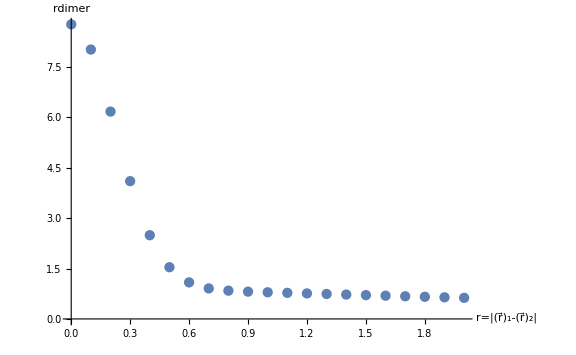

```mathematica
lambdaTest=8;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[3]];
dCores={{{6.381698039164151,10.560816794549673},{1.503314468672569,7.593839349710196},{0.23155449257199662,0.37216768804451095},{0.6531129664037622,0.031392341097770615}}};

NormTF[#]&/@dCores;

JacobiTrailWavefunctionU=Total[Abs[#[[1]]] Exp[-#[[2]] r1^2]&/@#]&/@dCores;rR=Range[0,2,0.100];
JacobiTrailWavefunctionDataU=Table[#/.{r1->R1},{R1,rR}]&/@JacobiTrailWavefunctionU;

plotData=Transpose[{rR,#}]&/@JacobiTrailWavefunctionDataU;

ListPlot[plotData,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},ImageSize->Large]
```

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.001;
(* Integration grid *)
rMa=12;
grdPerFermi=15;
nGrd=IntegerPart[rMa grdPerFermi];
results={};
(*dCores=Get["dimerCores_"<>ToString[lambdaTest]<>".dat"];*)
nbrOfCores=Length[dCores];
Do[
dimerCore=dCores[[nn]];

dimCore=Length[dimerCore];

tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,LECd,energ][[1]];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,dimCore,tmp}];
Print["core ",nn," )  λ=",lambdaTest," ; C_0(λ)=",LECc," ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; dim_d=",dimCore," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbar/√(Mm Abs[2.22]))];
,{nn,Length[dCores]}];
```

General::munfl: -0.000214326 (-5.80232×10^-307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -0.000214326 (-1.85652×10^-307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -0.000214326 (-9.05823×10^-306) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -0.000214326 (-6.28019×10^-307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -0.000214326 (-1.85652×10^-307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -0.000214326 (-1.3254×10^-306) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -0.000214326 (-5.16704×10^-308) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -0.000214326 (-9.00018×10^-308) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -0.000214326 (-9.05823×10^-306) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: -0.000214326 (-1.3254×10^-306) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: -0.000214326 (-1.3254×10^-306) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: -0.000214326 (-9.00018×10^-308) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

finite-difference runtime Δt = 0.228812 mins     p_match·r_max = 0.0833316

core 1 )  λ=8 ; C_0(λ)=-974.194 ; R_max=12 ; #=180 ; E_match=0.001 ; dim_d=4 ; a_dd=1.52375 ; a_dd/a_aa=0.352535

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

20.7369

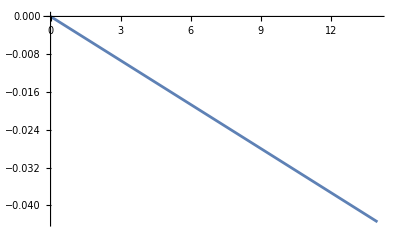

```mathematica
1/mh2
momFM=Sqrt[mh2 0.0002];
Plot[RiccatiBesselJ[momFM r,0]/RiccatiBesselN[momFM r,0](*-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin])*),{r,0,14}]
```

```mathematica
lambdaTest=10;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]]
LECd=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[3]]
```

-1206.46

-1256.76

214.608

finite-difference runtime Δt = 0.0144156 mins     p_match·r_max = 0.0208329

core 1 )  λ = 10   C_0(λ) = -1206.46   D_0(λ) = -1256.76     R_max = 3.     #(grid points) = 36                a_dd = 2.60966 fm        a_dd/a_aa = 0.603773

finite-difference runtime Δt = 0.0153097 mins     p_match·r_max = 0.024305

core 1 )  λ = 10   C_0(λ) = -1206.46   D_0(λ) = -1256.76     R_max = 3.5     #(grid points) = 42                a_dd = 2.27955 fm        a_dd/a_aa = 0.527399

finite-difference runtime Δt = 0.0259898 mins     p_match·r_max = 0.0277772

core 1 )  λ = 10   C_0(λ) = -1206.46   D_0(λ) = -1256.76     R_max = 4.     #(grid points) = 48                a_dd = -0.789794 fm        a_dd/a_aa = -0.182727

finite-difference runtime Δt = 0.026719 mins     p_match·r_max = 0.0312493

core 1 )  λ = 10   C_0(λ) = -1206.46   D_0(λ) = -1256.76     R_max = 4.5     #(grid points) = 54                a_dd = 14.0435 fm        a_dd/a_aa = 3.24911

finite-difference runtime Δt = 0.0280774 mins     p_match·r_max = 0.0347215

core 1 )  λ = 10   C_0(λ) = -1206.46   D_0(λ) = -1256.76     R_max = 5.     #(grid points) = 60                a_dd = 10.1747 fm        a_dd/a_aa = 2.35402

finite-difference runtime Δt = 0.0382856 mins     p_match·r_max = 0.0381936

core 1 )  λ = 10   C_0(λ) = -1206.46   D_0(λ) = -1256.76     R_max = 5.5     #(grid points) = 66                a_dd = 31.9148 fm        a_dd/a_aa = 7.38384

finite-difference runtime Δt = 0.0392364 mins     p_match·r_max = 0.0416658

core 1 )  λ = 10   C_0(λ) = -1206.46   D_0(λ) = -1256.76     R_max = 6.     #(grid points) = 72                a_dd = 2.22791 fm        a_dd/a_aa = 0.515451

finite-difference runtime Δt = 0.0500801 mins     p_match·r_max = 0.0451379

core 1 )  λ = 10   C_0(λ) = -1206.46   D_0(λ) = -1256.76     R_max = 6.5     #(grid points) = 78                a_dd = 4.47671 fm        a_dd/a_aa = 1.03573

finite-difference runtime Δt = 0.055726 mins     p_match·r_max = 0.0486101

core 1 )  λ = 10   C_0(λ) = -1206.46   D_0(λ) = -1256.76     R_max = 7.     #(grid points) = 84                a_dd = 5.22089 fm        a_dd/a_aa = 1.20791

finite-difference runtime Δt = 0.0626589 mins     p_match·r_max = 0.0520822

core 1 )  λ = 10   C_0(λ) = -1206.46   D_0(λ) = -1256.76     R_max = 7.5     #(grid points) = 90                a_dd = 5.61065 fm        a_dd/a_aa = 1.29808

finite-difference runtime Δt = 0.0705686 mins     p_match·r_max = 0.0555544

core 1 )  λ = 10   C_0(λ) = -1206.46   D_0(λ) = -1256.76     R_max = 8.     #(grid points) = 96                a_dd = 5.83326 fm        a_dd/a_aa = 1.34959

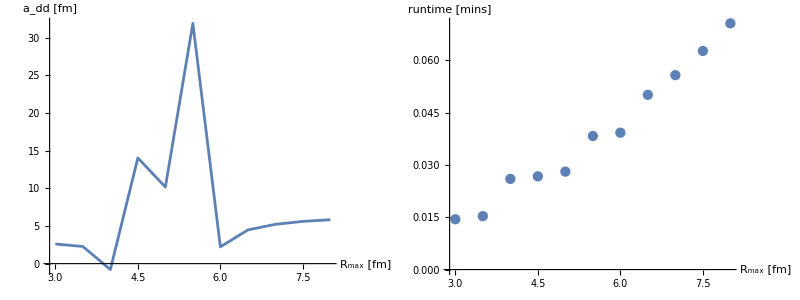

```mathematica
rMaxStart=3;
rMaxEnd=8;
nbrR=10;
coreNBR=1;
{e0Core,dimerCore}={-2.22,dCores[[coreNBR]]};
RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];
energ=0.001;
grdPerFermi=12;
results={};
resultsWF={};
runtimes={};
NormTF[dimerCore]
(*SetSharedVariable[results,resultsPhases];*)
Do[
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
{tmp,tmp2}=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,LECd,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[resultsWF,tmp2];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["core ",coreNBR," )  λ = ",lambdaTest,"   C_0(λ) = ",LECc,"   D_0(λ) = ",LECd,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{rMa,RmaxRange}]

Grid[{{ListPlot[Transpose[{RmaxRange,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
```

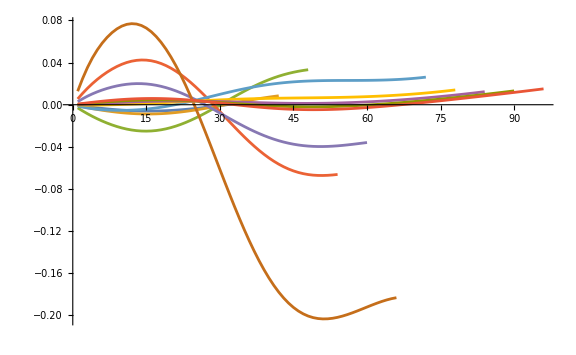

```mathematica
ListPlot[resultsWF,Joined->True,PlotRange->Full,ImageSize->Large]
```